```mathematica
(* JB *)
Remove["Global`*"]
ClearAll
FrontEndTokenExecute["DeleteGeneratedCells"]
```

```mathematica
(* import data from s.changeSeparation *)
SetDirectory[NotebookDirectory[]];
defaultSolutionFilePath=StringJoin[NotebookDirectory[],"../Output/s.changeSeparation"];
reloadDefaultSolutionFile[]:=(autoSols=reloadSolutionFile[defaultSolutionFilePath]);
Get[StringJoin[NotebookDirectory[],"/auto07pFilesParser.m"]];
```

```mathematica
reloadDefaultSolutionFile[];
```

** AUTO solution file has been parsed, with 320 snapshots found

```mathematica
(*number of snapshots*)
numSnapshots=autoSols //Length;
(* variable index *)
ithetaFunc=1;
iTauFunc=2;
(* parameter index *)
iε=1;
(* l = length of ribbon/width of ribbon *)
l= 300/18;
```

```mathematica
(* sorted parameters data
columns as: snapshot-number, ε, mExt, ||τ|| *)
paramData=Module[{paramsVec,labelSnapshots},
paramsVec=Transpose[kContinuationParams/.autoSols];
labelSnapshots= Transpose[Range[1,Length[paramsVec[[1]]]]];
Sort[Transpose[Join[{labelSnapshots},paramsVec]],#1[[2]]>#2[[2]]&]
];
FindSnapshotNearStrain[M_,x_]:=Module[{secondColumn,nearestElementIndex},
(*Get second column*)
secondColumn=M[[All,2]];
(*Find the index of the nearest element*)
nearestElementIndex=Position[secondColumn,(Nearest[secondColumn,x][[1]])][[1,1]];
(*Return the first element of the corresponding row*)
M[[nearestElementIndex,1]] ]
```

```mathematica
tauStar[ε_]=Piecewise[{{0, ε>-29.009999999999998},{ 2 √(10/3) √(-29.009999999999998-ε),ε<=-29.009999999999998}}];
tauStarData=tauStar/@paramData[[All,2]];
```

```mathematica
τRMS=ListLinePlot[Transpose[{-paramData[[All,2]],paramData[[All,4 ]]}],PlotStyle->{Black}];
analyticalTauStar=ListLinePlot[Transpose[{-paramData[[All,2]],tauStarData}],PlotStyle->{RGBColor[0.987259, 0.22707, 0.0290532]}];
```

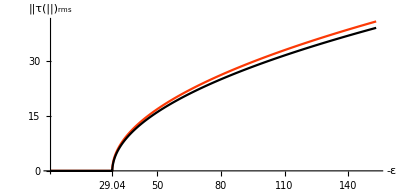

```mathematica
Show[analyticalTauStar,τRMS,BaseStyle->{FontFamily->"Times",FontSize->11},ImageSize->{400*(0.771/0.7)}, AspectRatio->(1/2.1),Ticks-> {{29.04,50,80,110,140},Automatic},TickLabels-> {All,All},PlotRangePadding->0,PlotRange-> {Automatic,{-2,Automatic}},
PlotStyle->{Thickness[0.005*(0.70/0.771)]},
AxesLabel->{"-ε","||τ(||)_rms"}]
```

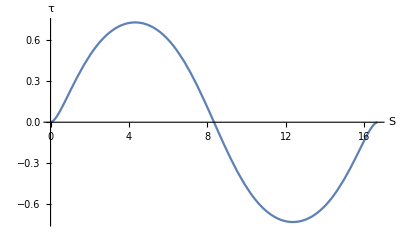

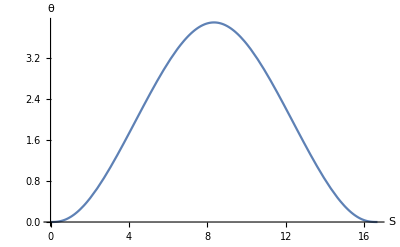

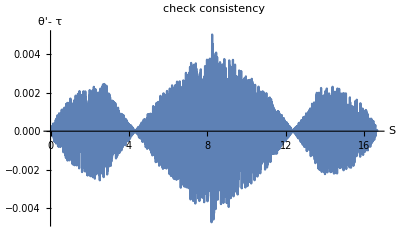

```mathematica
(* from paramData find snapshot near ε=-29.07 *)
snapshot=FindSnapshotNearStrain[paramData,-29.07];
sol=autoSols⟦snapshot⟧;
params= kContinuationParams/.sol;
ε= params[[iε]];
dat=kData/.sol;
sVec=l dat[[All,1]];
si=sVec[[1]];
sf=sVec[[Length[sVec]]];
τ=Interpolation[Transpose[{sVec,dat⟦All,iTauFunc+1⟧}],InterpolationOrder-> 1];
Plot[τ[S],{S,si,sf},AxesLabel->{"S","τ"}]
θ=Interpolation[Transpose[{sVec,dat⟦All,ithetaFunc+1⟧}],InterpolationOrder-> 1];
Plot[θ[S],{S,si,sf},AxesLabel->{"S","θ"}]
Plot[θ'[S]-τ[S],{S,si,sf},AxesLabel->{"S","θ'- τ"},PlotLabel->"check consistency"]
```